# Quadratic damping

```mathematica
m D[x[t],{t,2}]==-c D[x[t],t]^2-k x[t]
x''[t]==-α x'[t]^2-β x[t]
```

```mathematica
DSolve[ {dx[x]dx'[x]==-α dx[x]^2-β x,dx[1]==0},dx[x],x]
```

{{dx[x]→-(√(-(ⅇ^(-2 x α) (ⅇ^(2 α)-ⅇ^(2 x α)-2 ⅇ^(2 α) α+2 ⅇ^(2 x α) x α) β)/α^2))/(√2)},{dx[x]→(√(-(ⅇ^(-2 x α) (ⅇ^(2 α)-ⅇ^(2 x α)-2 ⅇ^(2 α) α+2 ⅇ^(2 x α) x α) β)/α^2))/(√2)}}

```mathematica
DSolve[x'[t]==ⅇ^(-x[t] α)/α √(β/2)√(ⅇ^(2 x[t] α)(1-2 x[t] α)+ ⅇ^(2 α) (2α-1)),x[t],t]
```

$Aborted

```mathematica
(* when over damping, dx < 0  and x > 0*)
(* When critical damping, dx = 0 and x = 0, at t-> ∞ *)
(* when under damping, dx = 0 has multiple solution *)
```

```mathematica
(√(-(ⅇ^(-2 x α) (ⅇ^(2 α)-ⅇ^(2 x α)-2 ⅇ^(2 α) α+2 ⅇ^(2 x α) x α) β)/α^2))/(√2)/.x->0//Simplify
```

(√(((1+ⅇ^(2 α) (-1+2 α)) β)/α^2))/(√2)

```mathematica
(* For critical damping *)
Solve[(1+ⅇ^(2 α) (-1+2 α)) β==0,α]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0}}

```mathematica
(* For α < β *)
x''[t]==-β x[t]
```

```mathematica
(* For α > β *)
x''[t]==-α x'[t]^2
```

```mathematica
DSolve[{y'[x]==-α y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(-x α)}}

```mathematica
DSolve[{x''[t]==-α x'[t]^2},x[t],t]
```

{{x[t]→C[2]+Log[t α-C[1]]/α}}

```mathematica
Solve[(1+ⅇ^(2 α) (-1+2 α))==0,α]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0}}

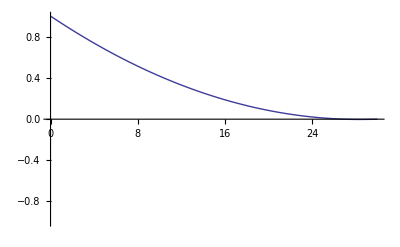

```mathematica
s=NDSolve[{x''[t]==-200x'[t]Abs[x'[t]]-1x[t],x[0]==1,x'[0]==0},x,{t,0,30}];
Plot[Evaluate[x[t]/.s],{t,0,30},PlotRange->{-1,1}]
```

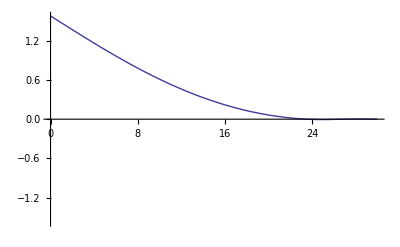

```mathematica
f=NDSolve[{x''[t]==-90x'[t]Abs[x'[t]]-1Sin[x[t]],x[0]==π/2,x'[0]==0},x,{t,0,30}];
Plot[Evaluate[x[t]/.f],{t,0,30},PlotRange->{-π/2,π/2}]
```

## Linear Damping

```mathematica
DSolve[{x''[t]==-ω^2 x[t],x[0]==a,x'[0]==0},x[t],t](* ω^2= k/m *)
```

{{x[t]→a Cos[t ω]}}

```mathematica
DSolve[{x''[t]==-α x'[t]-ω^2 x[t],x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→(-ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) α+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) α+ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) √(α^2-4 ω^2)+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) √(α^2-4 ω^2))/(2 √(α^2-4 ω^2))}}

```mathematica
(* For α > 2 ω *)
x[t]=ⅇ^(-(t α)/2) ( Cosh[1/2 t √(α^2-4 ω^2)]+α/(√(α^2-4 ω^2))Sinh[1/2 t √(α^2-4 ω^2)])
```

```mathematica
(* α = 2 ω *)
DSolve[{x''[t]==-2ω x'[t]-ω^2 x[t],x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→ⅇ^(-t ω) (1+t ω)}}

```mathematica
(* α < 2 ω *)
x[t]=ⅇ^(-(t α)/2) (Cos[1/2 t √(4 ω^2-α^2) ]+1/(√((4 ω^2)/α^2-1)) Sin[1/2 t √(4 ω^2-α^2) ])
```

```mathematica
Manipulate[
Plot[ {(-ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) α+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) α+ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) √(α^2-4 ω^2)+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) √(α^2-4 ω^2))/(2 √(α^2-4 ω^2)),ⅇ^(-t ω) (1+t ω),Exp[-1/2 t α],ⅇ^(-(t α)/2) Cos[1/2 t √(4 ω^2-α^2) ]},{t,0,10},PlotRange->{-1,1}],
{α,0,10,0.1},{ω,1,5}]
```

```mathematica
D[x[t],t]=
-ⅇ^(-(t α)/2)/2 Sin[1/2 t √(4 ω^2-α^2) ](1+4 ω^2-α^2)/(√(4 ω^2-α^2))
```

```mathematica
DSolve[{y'[x]y[x]==-α y[x]-ω^2 x},y[x],x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[-(α ArcTan[(α+(2 y[x])/x)/(√(-α^2+4 ω^2))])/(√(-α^2+4 ω^2))+1/2 Log[ω^2+(α y[x])/x+y[x]^2/x^2]==C[1]-Log[x],y[x]]

```mathematica
Manipulate[ParametricPlot[{(-ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) α+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) α+ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) √(α^2-4 ω^2)+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) √(α^2-4 ω^2))/(2 √(α^2-4 ω^2)),-ⅇ^(-(t α)/2)/2 Sin[1/2 t √(4 ω^2-α^2) ](1+4 ω^2-α^2)/(√(4 ω^2-α^2)) },{t,0,10},PlotRange->2],{α,0,10,0.1},{ω,1,5}]
```

```mathematica
Sinc[1/2 t √(4 ω^2-α^2)] 1/t
```

```mathematica
Manipulate[Plot[Sinc[1/2 t √(4 ω^2-α^2)] 1/t,{t,0,10},PlotRange->2],{α,0,10,0.1},{ω,1,5}]
```

## Quadratic since damping

```mathematica
(* For u[x] >=0 *)
DSolve[{u'[x]==-ω^2 Sin[x]/u[x]-α u[x],u[θ]==0},u[x],x]
```

{{u[x]→-√2 √((ⅇ^(-2 x α) ω^2 (ⅇ^(2 x α) Cos[x]-ⅇ^(2 α θ) Cos[θ]-2 ⅇ^(2 x α) α Sin[x]+2 ⅇ^(2 α θ) α Sin[θ]))/(1+4 α^2))},{u[x]→√2 √((ⅇ^(-2 x α) ω^2 (ⅇ^(2 x α) Cos[x]-ⅇ^(2 α θ) Cos[θ]-2 ⅇ^(2 x α) α Sin[x]+2 ⅇ^(2 α θ) α Sin[θ]))/(1+4 α^2))}}

```mathematica
(* For u[x] <= 0 *)
DSolve[{u'[x]==-ω^2 Sin[x]/u[x]+α u[x],u[θ]==0},u[x],x]
```

{{u[x]→-√2 √((ⅇ^(-2 α θ) ω^2 (ⅇ^(2 α θ) Cos[x]-ⅇ^(2 x α) Cos[θ]+2 ⅇ^(2 α θ) α Sin[x]-2 ⅇ^(2 x α) α Sin[θ]))/(1+4 α^2))},{u[x]→√2 √((ⅇ^(-2 α θ) ω^2 (ⅇ^(2 α θ) Cos[x]-ⅇ^(2 x α) Cos[θ]+2 ⅇ^(2 α θ) α Sin[x]-2 ⅇ^(2 x α) α Sin[θ]))/(1+4 α^2))}}

```mathematica
(1+4 α^2)/2 u[x]^2== (Cos[x]+2 α Sin[x]-ⅇ^(2 α (x-θ)) (Cos[θ]+2 α Sin[θ]))
```

```mathematica
ⅇ^(-2 α θ)  (ⅇ^(2 α θ) Cos[x]-ⅇ^(2 x α) Cos[θ]+2 ⅇ^(2 α θ) α Sin[x]-2 ⅇ^(2 x α) α Sin[θ])//FullSimplify
```

Cos[x]+2 α Sin[x]-ⅇ^(2 α (x-θ)) (Cos[θ]+2 α Sin[θ])

```mathematica
(* when over damping, dx < 0  and x > 0*)
(* When critical damping, dx = 0 and x = 0, at t-> ∞ *)
(* when under damping, dx = 0 has multiple solution *)
```

```mathematica
√2 √((ⅇ^(-2 x α) ω^2 (ⅇ^(2 x α) Cos[x]-ⅇ^(2 α θ) Cos[θ]-2 ⅇ^(2 x α) α Sin[x]+2 ⅇ^(2 α θ) α Sin[θ]))/(1+4 α^2))/.x->0
√2 √((ⅇ^(-2 α θ) ω^2 (ⅇ^(2 α θ) Cos[x]-ⅇ^(2 x α) Cos[θ]+2 ⅇ^(2 α θ) α Sin[x]-2 ⅇ^(2 x α) α Sin[θ]))/(1+4 α^2))/.x->0
```

√2 √((ω^2 (1-ⅇ^(2 α θ) Cos[θ]+2 ⅇ^(2 α θ) α Sin[θ]))/(1+4 α^2))

√2 √((ⅇ^(-2 α θ) ω^2 (ⅇ^(2 α θ)-Cos[θ]-2 α Sin[θ]))/(1+4 α^2))

```mathematica
Manipulate[Plot[{ⅇ^(2 α θ),Cos[θ]+2 α Sin[θ]},{θ,-π,π}],{α,0,10}]
```

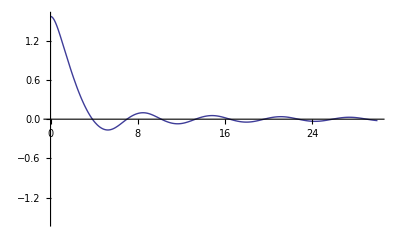

```mathematica
f=NDSolve[{x''[t]==-3x'[t]Abs[x'[t]]-1Sin[x[t]],x[0]==π/2,x'[0]==0},x,{t,0,30}];
Plot[Evaluate[x[t]/.f],{t,0,30},PlotRange->{-π/2,π/2}]
```

```mathematica
Manipulate[Plot[{√2 √((ⅇ^(-2 x α) (ⅇ^(2 x α) Cos[x]-ⅇ^(2 α θ) Cos[θ]-2 ⅇ^(2 x α) α Sin[x]+2 ⅇ^(2 α θ) α Sin[θ]))/(1+4 α^2)),-√2 √((ⅇ^(-2 α θ) (ⅇ^(2 α θ) Cos[x]-ⅇ^(2 x α) Cos[θ]+2 ⅇ^(2 α θ) α Sin[x]-2 ⅇ^(2 x α) α Sin[θ]))/(1+4 α^2))},{x,-π,π}],{α,0,10},{θ,0,π}]
```

```mathematica
(1+4 α^2)/2 u[x]^2== (Cos[x]+2 α Sin[x]-ⅇ^(2 α (x-θ)) (Cos[θ]+2 α Sin[θ]))
```

```mathematica
Manipulate[ContourPlot[{(1+4 α^2)/2 y^2== Cos[x]+2 α Sin[x]-ⅇ^(2 α (x-θ)) (Cos[θ]+2 α Sin[θ]),(1+4 α^2)/2 y^2==(1-ⅇ^(-2 α θ) Cos[θ]-2 ⅇ^(-2 α θ) α Sin[θ])+2 ⅇ^(-2 α θ) α (ⅇ^(2 α θ)-Cos[θ]-2 α Sin[θ]) x,(1+4 α^2)/2 y^2== Cos[x]-2 α Sin[x]-ⅇ^(2 α (θ-x))(Cos[θ]- α Sin[θ])},{x,-π,π},{y,-1,1},Axes->True],{α,0,10},{θ,0,π}]
```

```mathematica
Series[Sin[x+g]-ⅇ^(2 α (x-θ)) Sin[θ+g],{x,0,4}]
```

(Sin[g]-ⅇ^(-2 α θ) Sin[g+θ])+(Cos[g]-2 ⅇ^(-2 α θ) α Sin[g+θ]) x+(-Sin[g]/2-2 ⅇ^(-2 α θ) α^2 Sin[g+θ]) x^2+(-Cos[g]/6-4/3 ⅇ^(-2 α θ) α^3 Sin[g+θ]) x^3+(Sin[g]/24-2/3 ⅇ^(-2 α θ) α^4 Sin[g+θ]) x^4+O[x]^5

```mathematica
Series[ Cos[x]+2 α Sin[x]-ⅇ^(2 α (x-θ)) (Cos[θ]+2 α Sin[θ]),{x,0,4}]
```

(1-ⅇ^(-2 α θ) Cos[θ]-2 ⅇ^(-2 α θ) α Sin[θ])+2 ⅇ^(-2 α θ) α (ⅇ^(2 α θ)-Cos[θ]-2 α Sin[θ]) x+(-1/2-2 ⅇ^(-2 α θ) α^2 Cos[θ]-4 ⅇ^(-2 α θ) α^3 Sin[θ]) x^2-1/3 (ⅇ^(-2 α θ) α (ⅇ^(2 α θ)+4 α^2 Cos[θ]+8 α^3 Sin[θ])) x^3+1/24 ⅇ^(-2 α θ) (ⅇ^(2 α θ)-16 α^4 Cos[θ]-32 α^5 Sin[θ]) x^4+O[x]^5

```mathematica
(1+4 α^2)/2 y^2==(1-ⅇ^(-2 α θ) Cos[θ]-2 ⅇ^(-2 α θ) α Sin[θ])+2 ⅇ^(-2 α θ) α (ⅇ^(2 α θ)-Cos[θ]-2 α Sin[θ]) x
```

```mathematica
Manipulate[Plot[(1-ⅇ^(-2 α θ) Cos[θ]-2 ⅇ^(-2 α θ) α Sin[θ]),{θ,0,π},PlotRange->{0,2}],{α,0,100}]
```